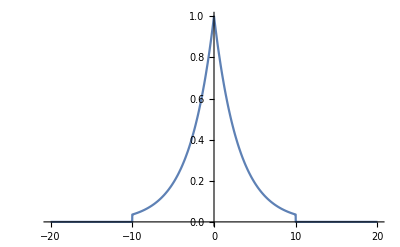

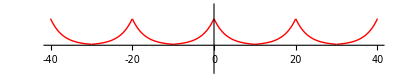

```mathematica
T = 10; to=3;
baseSignal[t_] := Exp[-Abs[t]/to]*UnitBox[t/(2T)];
rightSide[t_] := baseSignal[Mod[t,2T]];
leftSide[t_] := rightSide[-t]
periodicExtension[t_] = leftSide[t] + rightSide[t];
Plot[baseSignal[t],{t,-2T,2T},Exclusions->None]
Plot[periodicExtension[t],{t,-4T,4T},AspectRatio-> 0.2 ,PlotRange->{-1,1.5},
Ticks->{{-4T,-3T,-2T,-T,0,T,2T,3T,4T}},PlotStyle->{Thick,Red},ImageSize->Full]
```

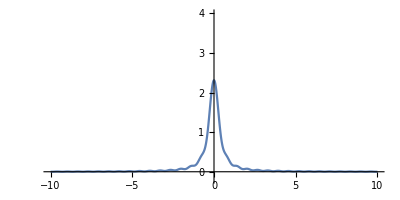

```mathematica
TF[w_] = FourierTransform[baseSignal[t],t,w];
Plot[TF[w],{w,-10,10},PlotRange->{{-10,10},{-0.2,4}},AspectRatio->0.5,ImageSize->Full]
```

```mathematica
energyTimeDomain = Integrate[Abs[(baseSignal[t])^2],{t,-T,T}];
Print["C'est l'énergie obtenue par la densité d'énergie temporel"]
Print[NumberForm[N[energyTimeDomain],10]];
```

C'est l'énergie obtenue par la densité d'énergie temporel

2.996182099

```mathematica
Print["Énergie obtenue par la densité spectrale d'énergie"]
frequencyEnergyDensity[w_] := (Abs[TF[w]])^2;
frequencyEnergy = 2 * NIntegrate[frequencyEnergyDensity[w],{w,0,10}];
Print[NumberForm[N[frequencyEnergy,10]]]
```

Énergie obtenue par la densité spectrale d'énergie

2.99605

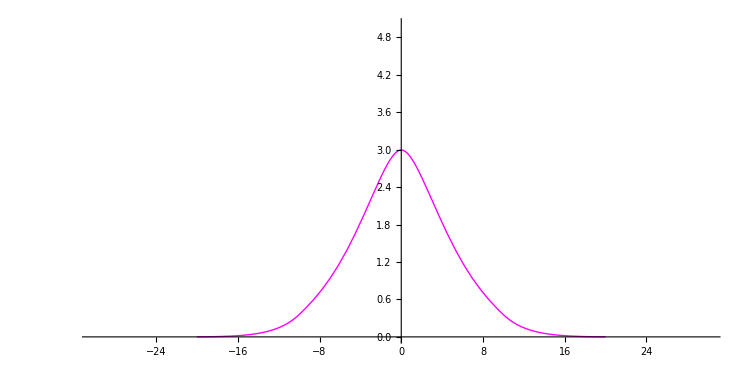

Vérification de la valeur d'énergie

2.99618

```mathematica
autoCorrelation[s_] := Integrate[baseSignal[t]*baseSignal[t-s],{t,-Infinity,Infinity}]
Plot[autoCorrelation[s],{s,-2T,2T},PlotRange->{{-30,30},{0,5}},AspectRatio->0.5,PlotStyle->{Magenta,Thick},ImageSize->{750,500}]
checkEnergy = N[autoCorrelation[0]];
Print["Vérification de la valeur d'énergie"]
Print[checkEnergy]
```

```mathematica
Print["Les Coefficients de Fourier"]
Alpha0 = FourierCosCoefficient[baseSignal[t],t,0];
AlphaN = FourierCosCoefficient[baseSignal[t],t,m];
Print[Alpha0]
Print[AlphaN]
```

Les Coefficients de Fourier

(6-6 ⅇ^(-π/3))/π

(6-6 (-1)^m ⅇ^(-π/3))/(π+9 m^2 π)

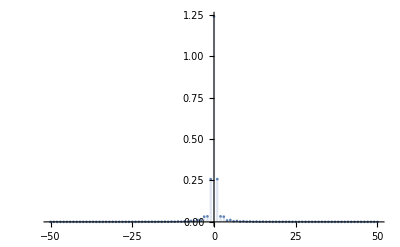

```mathematica
DiscretePlot[AlphaN,{m,-50,50},PlotRange->All,ImageSize->Full]
```

```mathematica
test[t_,N_] := Sum[AlphaN * Cos[m*Pi*t/T],{m,0,N}];
```

```mathematica
stepplot[N_] := Plot[test[t,N],{t,-10Pi,10Pi},ImageSize->{750,500},PlotRange->{0,1.75}];
```

```mathematica
Manipulate[stepplot[n],{n,0,70,1}]
```

```mathematica
MeanPower = (Integrate[(Abs[baseSignal[t]])^2,{t,-T,T}])/(2T);
Print["Puissace Moyenne du signal periodique"]
Print[N[MeanPower]]
```

Puissace Moyenne du signal periodique

0.149809

```mathematica
("Autre méthode")
```

Autre méthode

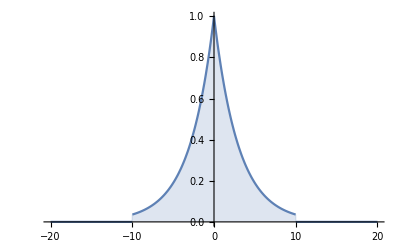

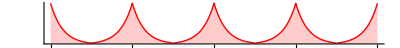

```mathematica
base=Exp[-Abs[t]/to]*UnitBox[(t)/(2T)];
Plot[base,{t,-2T,2T},Filling->Bottom]
Clear[k,n]
{k=0,n=4};
s=base;
Do[s+=Exp[-Abs[t+2k*T]/to]*UnitBox[(t+2k*T)/(2T)]+Exp[-Abs[t-2k*T]/to]*UnitBox[(t-2k*T)/(2T)],{k,n}]
Plot[s,{t,-4T, 4T},PlotRange->All,Filling->Bottom,AspectRatio-> 0.1 ,Ticks->{{-4T,-3T,-2T,-T,0,T,2T,3T,4T}},PlotStyle->{Thick,Red},ImageSize->Full]
```

(ⅇ^(-10/3-10 ⅈ ω) (-3+6 ⅇ^(10/3+10 ⅈ ω)+ⅇ^(20 ⅈ ω) (-3-9 ⅈ ω)+9 ⅈ ω))/(1+9 ω^2)

{(-6+6 ⅇ^(10/3))/(ⅇ^(10/3) (1+36 π^2)),(-6+6 ⅇ^(10/3))/(ⅇ^(10/3) (1+144 π^2)),(-6+6 ⅇ^(10/3))/(ⅇ^(10/3) (1+324 π^2)),(-6+6 ⅇ^(10/3))/(ⅇ^(10/3) (1+576 π^2)),(-6+6 ⅇ^(10/3))/(ⅇ^(10/3) (1+900 π^2))}

{(3 (-2+2 ⅇ^(10/3)))/(ⅇ^(10/3) (1+36 π^2)),(3 (-2+2 ⅇ^(10/3)))/(ⅇ^(10/3) (1+144 π^2)),(3 (-2+2 ⅇ^(10/3)))/(ⅇ^(10/3) (1+324 π^2)),(3 (-2+2 ⅇ^(10/3)))/(ⅇ^(10/3) (1+576 π^2)),(3 (-2+2 ⅇ^(10/3)))/(ⅇ^(10/3) (1+900 π^2))}

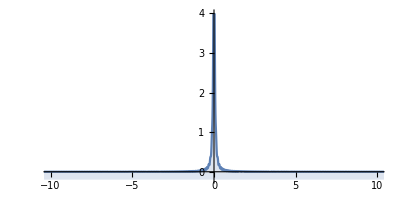

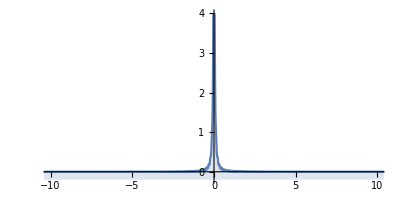

{(ⅇ^(-10/3+10 Im[w]) Abs[(-3+6 ⅇ^(10/3+10 ⅈ w)+ⅇ^(20 ⅈ w) (-3-9 ⅈ w)+9 ⅈ w)/(1+9 w^2)])/(√(2 π)),(ⅇ^(-10/3+10 Im[w]) Abs[(-3+6 ⅇ^(10/3+10 ⅈ w)+ⅇ^(20 ⅈ w) (-3-9 ⅈ w)+9 ⅈ w)/(1+9 w^2)])/(√(2 π)),(ⅇ^(-10/3+10 Im[w]) Abs[(-3+6 ⅇ^(10/3+10 ⅈ w)+ⅇ^(20 ⅈ w) (-3-9 ⅈ w)+9 ⅈ w)/(1+9 w^2)])/(√(2 π)),(ⅇ^(-10/3+10 Im[w]) Abs[(-3+6 ⅇ^(10/3+10 ⅈ w)+ⅇ^(20 ⅈ w) (-3-9 ⅈ w)+9 ⅈ w)/(1+9 w^2)])/(√(2 π)),(ⅇ^(-10/3+10 Im[w]) Abs[(-3+6 ⅇ^(10/3+10 ⅈ w)+ⅇ^(20 ⅈ w) (-3-9 ⅈ w)+9 ⅈ w)/(1+9 w^2)])/(√(2 π))}

-Graphics-

```mathematica
Animate[Plot[Exp[-Abs[t-a]/to]*UnitBox[(t-a)/(2T)],{t,-20,20},PlotStyle->{Thickness[0.005]},PlotRange->{0,1},Filling->Bottom],{T,13,0.5,1},{a,-10,10},AnimationRunning->False]
Clear[ω,f]
Q = FourierTransform[Sqrt[2*π] baseSignal[t],t,ω]
ω=2π*f;
Table[Abs[Q],{f,1,5}]
tf=∫_(-∞)^∞ baseSignal[t]*E^(-I*2*π*f*t)ⅆt;
Table[Abs[tf],{f,1,5}]
Plot[tf,{f,-20,20},PlotRange -> {{-10, 10}, {-0.2, 4}},Filling->Bottom, AspectRatio -> 0.5, ImageSize -> Full]
Plot[Q,{f,-20,20},PlotRange -> {{-10, 10}, {-0.2, 4}},Filling->Bottom, AspectRatio -> 0.5, ImageSize -> Full]
TF[w_] = FourierTransform[ baseSignal[t], t, w];
Table[Abs[TF[w]], {f, 1, 5}]
Plot[TF[w], {w, -10, 10}, PlotRange -> {{-10, 10}, {-0.2, 4}}, 
   AspectRatio -> 0.5, ImageSize -> Full]
```

```mathematica
base=Exp[-Abs[t]/to]*UnitBox[(t)/(2T)];
energie=∫_(-∞)^∞ Abs[base]^2 ⅆt
Print[NumberForm[N[energie],10]];
```

(3 (-1+ⅇ^(20/3)))/ⅇ^(20/3)

2.996182099

this is frequency domain

(ⅇ^(-10/3-10 ⅈ ω) (-3+6 ⅇ^(10/3+10 ⅈ ω)+ⅇ^(20 ⅈ ω) (-3-9 ⅈ ω)+9 ⅈ ω))/(1+9 ω^2)

ⅇ^(-20/3+20 Im[ω]) Abs[((-3+6 ⅇ^(10/3+10 ⅈ ω)+ⅇ^(20 ⅈ ω) (-3-9 ⅈ ω)+9 ⅈ ω)^2)/((1+9 ω^2)^2)]

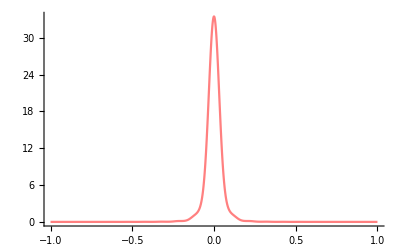

this is power average

(3 (-1+ⅇ^(20/3)))/(20 ⅇ^(20/3))

(3 (-1+ⅇ^(20/3)))/(20 ⅇ^(20/3))

0.1498091049

0.1498091049

```mathematica
Print["this is frequency domain"]
Clear[ω]
Q=FourierTransform[Sqrt[2*π] base,t,ω]
Densite=Abs[(Q)^2]
ω=2π*f;
Densite;
Plot[Abs[Densite],{f,-1,1},PlotStyle->Pink,PlotRange->All]
Print["this is power average"]
puissance=(1/(2T))*∫_(-∞)^∞ Abs[base]^2 ⅆt
puissance2=energie/(2T)
Print[NumberForm[N[puissance],10]];
Print[NumberForm[N[puissance2],10]];
```

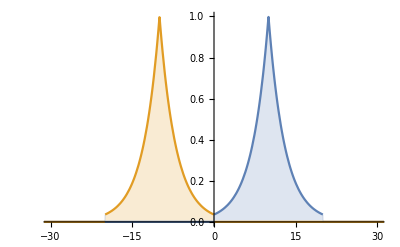

Piecewise[{{3 ⅇ^(-20/3-τ/3) (ⅇ^(20/3)-ⅇ^(2 τ/3)), τ==0}, {-ⅇ^(-τ/3) (-20+τ), 10<τ<20}, {ⅇ^(-τ/3) τ, τ==10}, {-ⅇ^(τ/3) τ, τ==-10}, {ⅇ^(τ/3) (20+τ), -20<τ<-10}, {ⅇ^(-20/3-τ/3) (3 ⅇ^(20/3)-3 ⅇ^(2 τ/3)+ⅇ^(20/3) τ), 0<τ<10}, {-ⅇ^(-20/3-τ/3) (3-3 ⅇ^(20/3+(2 τ)/3)+ⅇ^(20/3+(2 τ)/3) τ), -10<τ<0}, {0, True}}]

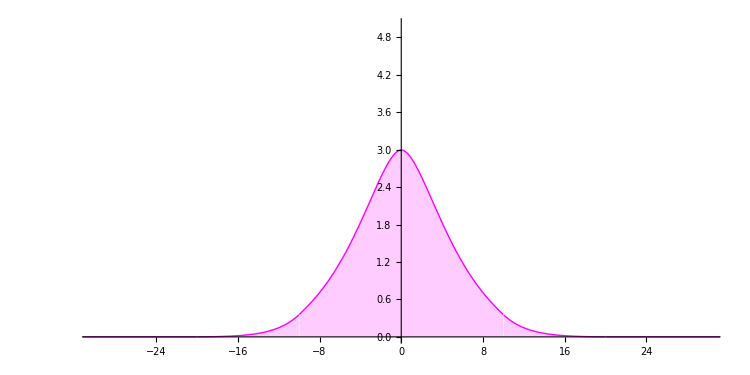

(Piecewise[{{3. 2.718281828^(-6.666666667-0.3333333333 τ) (785.7719942-1. 2.718281828^(0.6666666667 τ)), τ==0.}, {-1. 2.718281828^(-0.3333333333 τ) (-20.+τ), 10.<τ<20.}, {2.718281828^(-0.3333333333 τ) τ, τ==10.}, {-1. 2.718281828^(0.3333333333 τ) τ, τ==-10.}, {2.718281828^(0.3333333333 τ) (20.+τ), -20.<τ<-10.}, {2.718281828^(-6.666666667-0.3333333333 τ) (2357.315983-3. 2.718281828^(0.6666666667 τ)+785.7719942 τ), 0.<τ<10.}, {-1. 2.718281828^(-6.666666667-0.3333333333 τ) (3.-3. 2.718281828^(6.666666667+0.6666666667 τ)+2.718281828^(6.666666667+0.6666666667 τ) τ), -10.<τ<0.}, {0., True}}])[0.]

```mathematica
base =Exp[-Abs[t-T]/to]*UnitBox[(t-T)/(2T)];
baseauto=Exp[-Abs[t+T]/to]*UnitBox[(t+T)/(2T)];
Plot[{base,baseauto},{t,-4T,4T},Filling->Bottom,PlotRange->{{-30,30},{0,1}}]
Γ=Convolve[base,baseauto, t,τ]
Plot[Γ,{τ,-4T,4T},Filling->Bottom,PlotRange->{{-30,30},{0,5}},AspectRatio->0.5,PlotStyle->{Magenta,Thick},ImageSize->{750,500}] 

Print[NumberForm[N[Γ[0]],10]];
```

```mathematica
Clear[n]

alpha=(2/(2T))*∫_0^(+2T) base*Cos[2*π*n*t/(2T)]ⅆt;
alpha0=(2/(2T))*∫_0^(+2T) base ⅆt;
beta=(2/(2T))*∫_0^(+2T) base*Sin[2*π*n*t/(2T)]ⅆt;
Table[beta,{n,1,5}]
Table[alpha,{n,1,5}]
Alpha0 = FourierCosCoefficient[baseSignal[t],t,0];
AlphaN = FourierCosCoefficient[baseSignal[t],t,n];
Print[Alpha0]
Print[AlphaN]
```

{0,0,0,0,0}

{(3 (-20-20 ⅇ^(10/3)))/(ⅇ^(10/3) (100+9 π^2)),(3 (-20+20 ⅇ^(10/3)))/(ⅇ^(10/3) (100+36 π^2)),(3 (-20-20 ⅇ^(10/3)))/(ⅇ^(10/3) (100+81 π^2)),(3 (-20+20 ⅇ^(10/3)))/(ⅇ^(10/3) (100+144 π^2)),(3 (-20-20 ⅇ^(10/3)))/(ⅇ^(10/3) (100+225 π^2))}

(6-6 ⅇ^(-π/3))/π

(6-6 (-1)^n ⅇ^(-π/3))/(π+9 n^2 π)